General::ovfl: Overflow occurred in computation.

General::stop: Further output of General :: ovfl will be suppressed during this calculation.

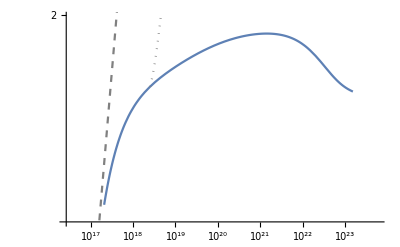

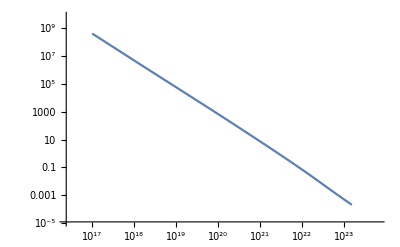

InterpolatingFunction::dmval: Input value {Overflow[]} lies outside the range of data in the interpolating function. Extrapolation will be used.

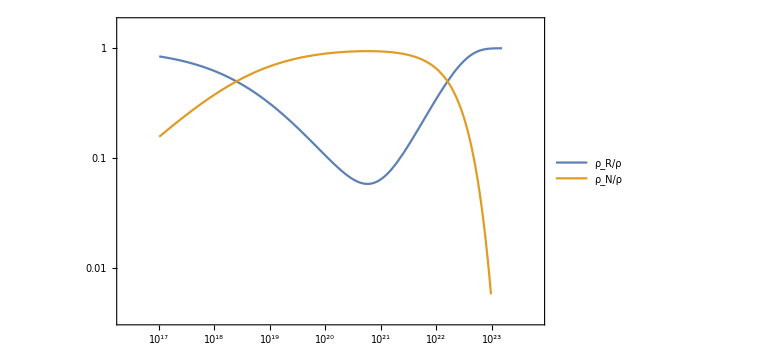
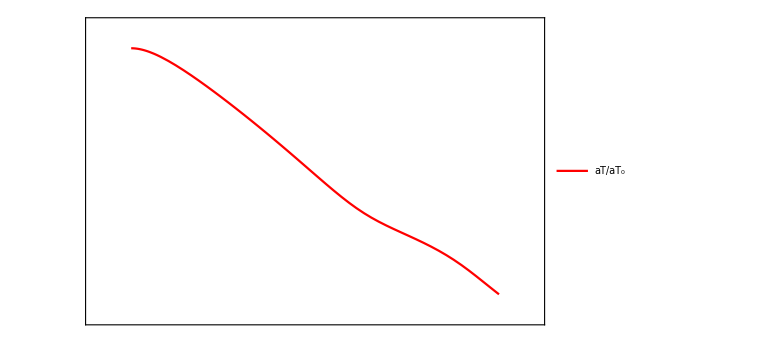

```mathematica
Block[{M,m,Γ,H,ρ,τ,T,g,n,t},(
M=1.22 10^22;
Subscript[m, N]=50;
τ=10; (*sec*)
Γ=τ^-1 6.58 10^-22;
H[t_]:=√((8π)/(3 M^2)(Subscript[ρ, R][t]+Subscript[ρ, N][t]));
Hsol[sol_]:=√((8π)/(3 M^2)Total[sol/.t->#])&;
Subscript[n, N][T_]:=(Subscript[m, N]/(2π T))^(3/2)E^(-Subscript[m, N]/T);
ρ[T_,g_]:=π^2/30 g T^4;
t[T_,g_]:=0.301 g^(-1/2)M T^-2;
T=100;
g=10.75;

t0=t[T,g+2];
t1=t0+(10τ)/(6.58 10^-22);

Subscript[ρ, N0]=ρ[T,2](*Subscript[m, N] Subscript[n, N][T]*);
Subscript[ρ, R0]=ρ[T,g];
a[t_,H_]:=E^If[t== t0,0,NIntegrate[H[tt],{tt,t0,t}]];

sol={Subscript[ρ, R][t],Subscript[ρ, N][t]}/.First[NDSolve[{
D[Subscript[ρ, R][t], t]+4H[t] Subscript[ρ, R][t]==Γ Subscript[ρ, N][t],
D[Subscript[ρ, N][t], t]+3H[t] Subscript[ρ, N][t]==-Γ Subscript[ρ, N][t],
Subscript[ρ, N][t0]==Subscript[ρ, N0],
Subscript[ρ, R][t0]==Subscript[ρ, R0]
},{Subscript[ρ, R],Subscript[ρ, N]},{t,t0,t1}]
];

teq=t/.FindRoot[sol⟦1⟧==sol⟦2⟧,{t,t0}];
Print[Show[{
LogLogPlot[a[t,Hsol[sol]],{t,t0,t1}],
LogLogPlot[{
(t/t0)^(1/2),
If[t<teq,0,a[teq,Hsol[sol]](t/teq)^(2/3)]
},{t,t0,t1},PlotStyle->{{Gray,Dashed},{Gray,Dotted}}]
}]];
Print[LogLogPlot[Total[sol],{t,t0,t1}]];
Overlay[{
LogLogPlot[Evaluate[sol/Total[sol]],{t,t0,t1},PlotLegends->{"ρ_R/ρ","ρ_N/ρ"},
ImageSize->Large,ImagePadding->35,Frame->{True,True,True,False},FrameStyle->{Automatic,Blue,Automatic,Automatic}],
LogLogPlot[(a[t,Hsol[sol]](sol⟦1⟧/(π^2/30 g))^(1/4))/T,{t,t0,t1},
ImageSize->Large,PlotStyle->Red,ImagePadding->35,Axes->False,Frame->{False,False,False,True},FrameTicks->{None,None,None,All},FrameStyle->{Automatic,Automatic,Automatic,Red},PlotLegends->{"aT/aT_0"}]
}]
)]
```